# Доска Гальтона

Выполнила студентка ММФ БГУ
КМ, 1 к, 5 гр. Ковалевская В.С.
  14 октября 2021

## Моделирование доски

### Задание 1

Реализуйте функцию для нахождения координат точек доски Гальтона.

```mathematica
v1={-1/2, -(√3)/2};
v2={1, 0};
galt[1]={{{0,0}}};
```

```mathematica
(galt[1]//Last//First)+v1
```

{-1/2,-(√3)/2}

```mathematica
NestList[#+v2&,(galt[1]//Last//First)+v1,1]
```

{{-1/2,-(√3)/2},{1/2,-(√3)/2}}

```mathematica
Append[galt[1],NestList[#+v2&,(galt[1]//Last//First)+v1,1]]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}}}

Рекурсией находим координаты. galt[1]={{{0,0}}} - база, а далее от первой точки (n-1)-го уровня сдвигаемся вниз на v1 и затем от неё сдвигаемся вправо на v2.

```mathematica
ClearAll[galt];
galt[1]={{{0,0}}};
galt[n_Integer?Positive]:=Append[galt[n-1],NestList[#+v2&,(galt[n-1]//Last//First)+v1,n-1]];
```

Функция galt[n_Integer?Positive]  для заданного размера  доски Гальтона возвращает координаты точек доски.
Вход: размер доски.
Выход: координаты точек - список списков.

```mathematica
galt[5]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}},{{-3/2,-(3 √3)/2},{-1/2,-(3 √3)/2},{1/2,-(3 √3)/2},{3/2,-(3 √3)/2}},{{-2,-2 √3},{-1,-2 √3},{0,-2 √3},{1,-2 √3},{2,-2 √3}}}

```mathematica
galt[10]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}},{{-3/2,-(3 √3)/2},{-1/2,-(3 √3)/2},{1/2,-(3 √3)/2},{3/2,-(3 √3)/2}},{{-2,-2 √3},{-1,-2 √3},{0,-2 √3},{1,-2 √3},{2,-2 √3}},{{-5/2,-(5 √3)/2},{-3/2,-(5 √3)/2},{-1/2,-(5 √3)/2},{1/2,-(5 √3)/2},{3/2,-(5 √3)/2},{5/2,-(5 √3)/2}},{{-3,-3 √3},{-2,-3 √3},{-1,-3 √3},{0,-3 √3},{1,-3 √3},{2,-3 √3},{3,-3 √3}},{{-7/2,-(7 √3)/2},{-5/2,-(7 √3)/2},{-3/2,-(7 √3)/2},{-1/2,-(7 √3)/2},{1/2,-(7 √3)/2},{3/2,-(7 √3)/2},{5/2,-(7 √3)/2},{7/2,-(7 √3)/2}},{{-4,-4 √3},{-3,-4 √3},{-2,-4 √3},{-1,-4 √3},{0,-4 √3},{1,-4 √3},{2,-4 √3},{3,-4 √3},{4,-4 √3}},{{-9/2,-(9 √3)/2},{-7/2,-(9 √3)/2},{-5/2,-(9 √3)/2},{-3/2,-(9 √3)/2},{-1/2,-(9 √3)/2},{1/2,-(9 √3)/2},{3/2,-(9 √3)/2},{5/2,-(9 √3)/2},{7/2,-(9 √3)/2},{9/2,-(9 √3)/2}}}

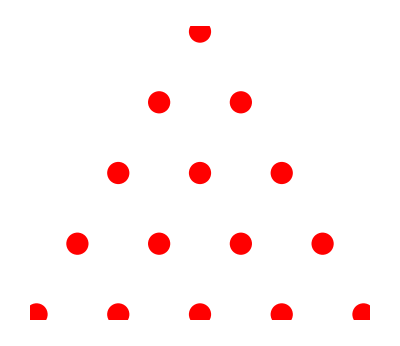

```mathematica
Graphics[{Red,PointSize@0.04,galt[5]//Map[Point]}]
```

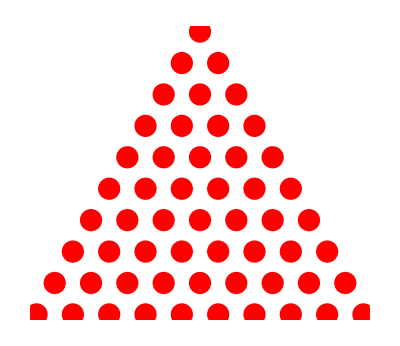

```mathematica
Graphics[{Red,PointSize@0.04,galt[10]//Map[Point]}]
```

## Задание 2

```mathematica
{Append[#,Last[#]],Append[#,Last[#]+1](*каждый следующий шаг шарик опускается на один ряд вниз*)}&/@{{1}}
```

{{{1,1},{1,2}}}

```mathematica
{{{1,1},{1,2}}}//Flatten[#,1]&
```

{{1,1},{1,2}}

```mathematica
{Append[#,Last[#]],Append[#,Last[#]+1]}&/@{{1,1},{1,2}}
```

{{{1,1,1},{1,1,2}},{{1,2,2},{1,2,3}}}

```mathematica
{Append[#,Last[#]],Append[#,Last[#]+1]}&/@{{{1,1,1},{1,1,2}},{{1,2,2},{1,2,3}}}
```

{{{{1,1,1},{1,1,2},{1,1,2}},{{1,1,1},{1,1,2},{2,2,3}}},{{{1,2,2},{1,2,3},{1,2,3}},{{1,2,2},{1,2,3},{2,3,4}}}}

```mathematica
{Append[#,Last[#]],Append[#,Last[#]+1]}&/@{{1}}//Flatten[#,1]&
```

{{1,1},{1,2}}

```mathematica
{Append[#,Last[#]],Append[#,Last[#]+1]}&/@{{1,1},{1,2}}//Flatten[#,1]&
```

{{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
ClearAll[giveAllRoutes];
giveAllRoutes[n_Integer?Positive]:=Nest[({Append[#,Last[#]],Append[#,Last[#]+1]}&/@#//Flatten[#,1]&)&,{{1}},n-1]
```

Функция giveAllRoutes
Вход: размер доски.
Выход: всевозможные пути падения шарика.

```mathematica
giveAllRoutes[3]
```

{{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
giveAllRoutes[5]
```

{{1,1,1,1,1},{1,1,1,1,2},{1,1,1,2,2},{1,1,1,2,3},{1,1,2,2,2},{1,1,2,2,3},{1,1,2,3,3},{1,1,2,3,4},{1,2,2,2,2},{1,2,2,2,3},{1,2,2,3,3},{1,2,2,3,4},{1,2,3,3,3},{1,2,3,3,4},{1,2,3,4,4},{1,2,3,4,5}}

```mathematica
RandomChoice[%]
```

{1,2,3,3,3}

```mathematica
giveAllRoutes[1]
```

{{1}}

```mathematica
giveAllRoutes[2]
```

{{1,1},{1,2}}

```mathematica
giveAllRoutes[3]
```

{{1,1,1},{1,1,2},{1,2,2},{1,2,3}}

```mathematica
giveAllRoutes[5]
```

{{1,1,1,1,1},{1,1,1,1,2},{1,1,1,2,2},{1,1,1,2,3},{1,1,2,2,2},{1,1,2,2,3},{1,1,2,3,3},{1,1,2,3,4},{1,2,2,2,2},{1,2,2,2,3},{1,2,2,3,3},{1,2,2,3,4},{1,2,3,3,3},{1,2,3,3,4},{1,2,3,4,4},{1,2,3,4,5}}

```mathematica
RandomChoice@giveAllRoutes[5]
```

{1,2,2,3,3}

```mathematica
n=21(*кол-во падений*);
pointRoutes=Table[RandomChoice@giveAllRoutes[5],{n}]
pointFinals=Last/@pointRoutes
Table[Count[%,i],{i,1,5}]
```

{{1,1,1,2,2},{1,2,3,4,5},{1,2,3,3,3},{1,2,3,4,4},{1,1,1,1,2},{1,2,3,3,4},{1,2,3,3,3},{1,2,2,2,2},{1,2,3,3,4},{1,2,3,3,3},{1,2,2,3,4},{1,2,3,4,5},{1,1,2,3,4},{1,1,1,2,2},{1,1,1,2,2},{1,2,2,2,2},{1,1,1,1,1},{1,2,3,3,4},{1,2,2,2,3},{1,1,1,1,2},{1,2,3,3,4}}

{2,5,3,4,2,4,3,2,4,3,4,5,4,2,2,2,1,4,3,2,4}

{1,7,4,7,2}

```mathematica
Table[Count[Take[pointFinals,i],#]&/@Range[5],{i,1,n}]
```

{{0,1,0,0,0},{0,1,0,0,1},{0,1,1,0,1},{0,1,1,1,1},{0,2,1,1,1},{0,2,1,2,1},{0,2,2,2,1},{0,3,2,2,1},{0,3,2,3,1},{0,3,3,3,1},{0,3,3,4,1},{0,3,3,4,2},{0,3,3,5,2},{0,4,3,5,2},{0,5,3,5,2},{0,6,3,5,2},{1,6,3,5,2},{1,6,3,6,2},{1,6,4,6,2},{1,7,4,6,2},{1,7,4,7,2}}

```mathematica
board=galt[5]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}},{{-3/2,-(3 √3)/2},{-1/2,-(3 √3)/2},{1/2,-(3 √3)/2},{3/2,-(3 √3)/2}},{{-2,-2 √3},{-1,-2 √3},{0,-2 √3},{1,-2 √3},{2,-2 √3}}}

```mathematica
ReplacePart[pointRoutes,{i_,j_}:>board[[j,pointRoutes[[i,j]]]]]
```

{{{0,0},{1/2,-(√3)/2},{1,-√3},{1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{1/2,-(√3)/2},{1,-√3},{3/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3}},{{0,0},{1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{1/2,-(√3)/2},{1,-√3},{3/2,-(3 √3)/2},{2,-2 √3}},{{0,0},{-1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-3/2,-(3 √3)/2},{-2,-2 √3}},{{0,0},{-1/2,-(√3)/2},{0,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3}},{{0,0},{1/2,-(√3)/2},{1,-√3},{1/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{-1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-3/2,-(3 √3)/2},{-2,-2 √3}},{{0,0},{-1/2,-(√3)/2},{-1,-√3},{-1/2,-(3 √3)/2},{-1,-2 √3}},{{0,0},{1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{1/2,-(√3)/2},{0,-√3},{1/2,-(3 √3)/2},{0,-2 √3}},{{0,0},{1/2,-(√3)/2},{1,-√3},{1/2,-(3 √3)/2},{1,-2 √3}},{{0,0},{1/2,-(√3)/2},{1,-√3},{3/2,-(3 √3)/2},{2,-2 √3}}}

```mathematica
linii=ReplacePart[pointRoutes,{i_,j_}:>board[[j,pointRoutes[[i,j]]]]]//Last
```

{{0,0},{1/2,-(√3)/2},{1,-√3},{3/2,-(3 √3)/2},{2,-2 √3}}

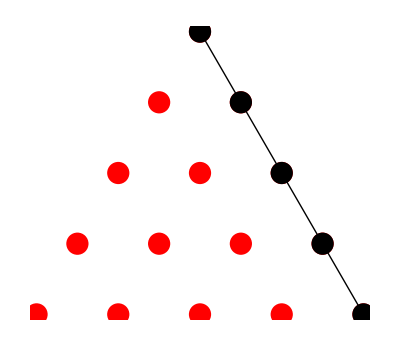

```mathematica
Graphics[{{Red,PointSize@0.04,galt[5]//Map[Point]},{Black,Line[linii],PointSize@0.04,linii//Map[Point]}}]
```

### Задание 3.

Использую функции Graphiсs и ListAnimate. Реализуйте анимацию последовательного поступления некоторого количества шариков на доску заданного размера.

```mathematica
board=galt[5]
```

{{{0,0}},{{-1/2,-(√3)/2},{1/2,-(√3)/2}},{{-1,-√3},{0,-√3},{1,-√3}},{{-3/2,-(3 √3)/2},{-1/2,-(3 √3)/2},{1/2,-(3 √3)/2},{3/2,-(3 √3)/2}},{{-2,-2 √3},{-1,-2 √3},{0,-2 √3},{1,-2 √3},{2,-2 √3}}}

```mathematica
waysCoord=ReplacePart[pointRoutes,{i_,j_}:>board[[j,pointRoutes[[i,j]]]]];
```

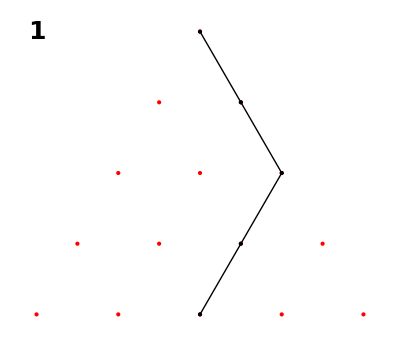
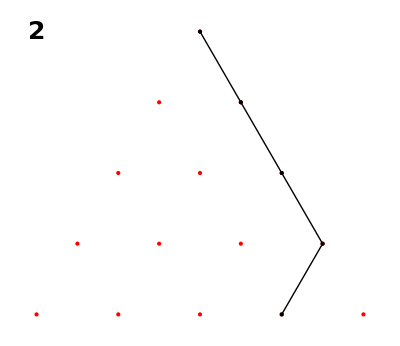
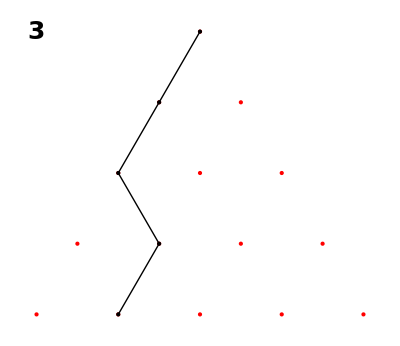
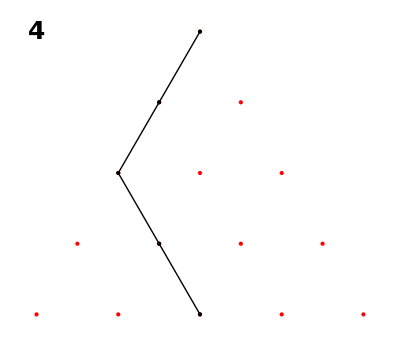
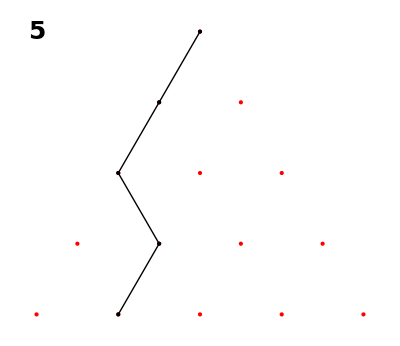
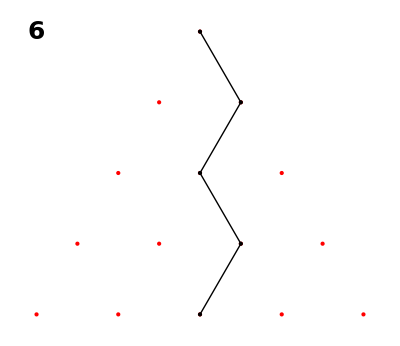
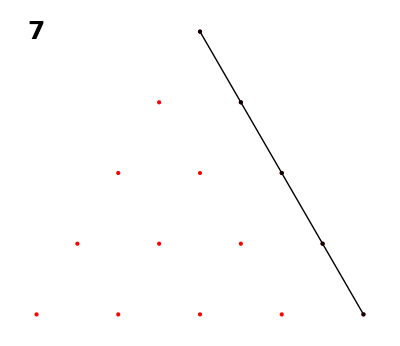
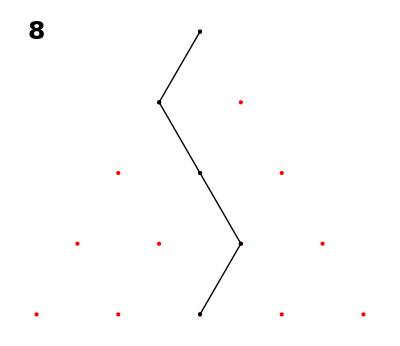

```mathematica
Table[Graphics[
{Text[Style[i,Bold,25],{-2,0}],
{Red,Point[#]&/@#}&/@board,
Black,Point[waysCoord[[i]]],
Black,Line[waysCoord[[i]]]},
BaseStyle->{PointSize[0.03]}],
{i,1,Length@waysCoord}]
```

```mathematica
Table[MapThread[Text[Style[#1,Magenta,Bold,15],#2]&,
{Count[Take[pointFinals,i],#]&/@Range[5],
#+{0,-1}&/@Last[board]}],{i,1,Length@waysCoord}]
```

{{Text[0,{-2,-1-2 √3}],Text[1,{-1,-1-2 √3}],Text[0,{0,-1-2 √3}],Text[0,{1,-1-2 √3}],Text[0,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[1,{-1,-1-2 √3}],Text[0,{0,-1-2 √3}],Text[0,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[1,{-1,-1-2 √3}],Text[1,{0,-1-2 √3}],Text[0,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[1,{-1,-1-2 √3}],Text[1,{0,-1-2 √3}],Text[1,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[2,{-1,-1-2 √3}],Text[1,{0,-1-2 √3}],Text[1,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[2,{-1,-1-2 √3}],Text[1,{0,-1-2 √3}],Text[2,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[2,{-1,-1-2 √3}],Text[2,{0,-1-2 √3}],Text[2,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[2,{0,-1-2 √3}],Text[2,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[2,{0,-1-2 √3}],Text[3,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[3,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[4,{1,-1-2 √3}],Text[1,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[4,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[3,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[5,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[4,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[5,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[5,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[5,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[0,{-2,-1-2 √3}],Text[6,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[5,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[1,{-2,-1-2 √3}],Text[6,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[5,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[1,{-2,-1-2 √3}],Text[6,{-1,-1-2 √3}],Text[3,{0,-1-2 √3}],Text[6,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[1,{-2,-1-2 √3}],Text[6,{-1,-1-2 √3}],Text[4,{0,-1-2 √3}],Text[6,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[1,{-2,-1-2 √3}],Text[7,{-1,-1-2 √3}],Text[4,{0,-1-2 √3}],Text[6,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]},{Text[1,{-2,-1-2 √3}],Text[7,{-1,-1-2 √3}],Text[4,{0,-1-2 √3}],Text[7,{1,-1-2 √3}],Text[2,{2,-1-2 √3}]}}

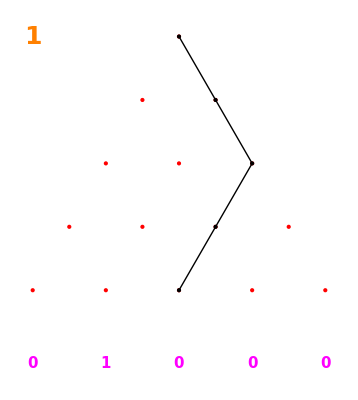
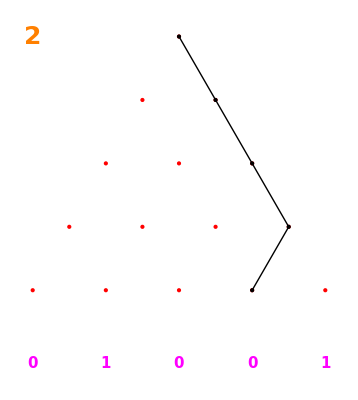
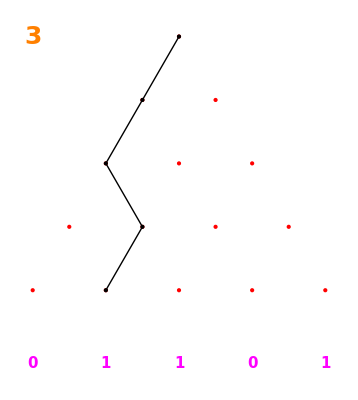
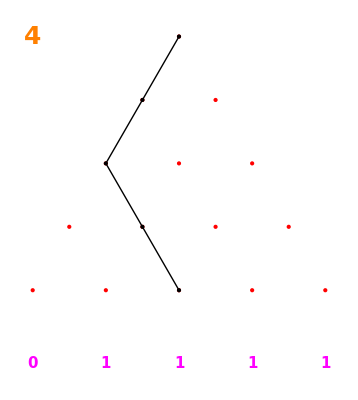
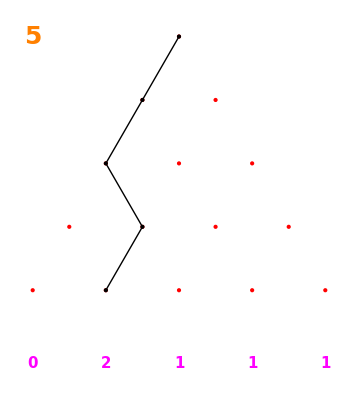
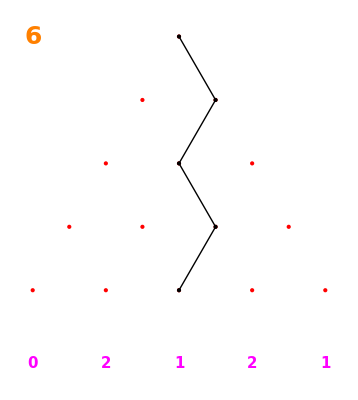
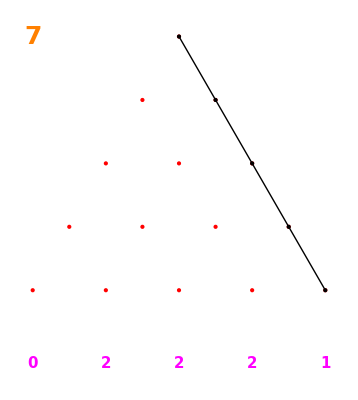
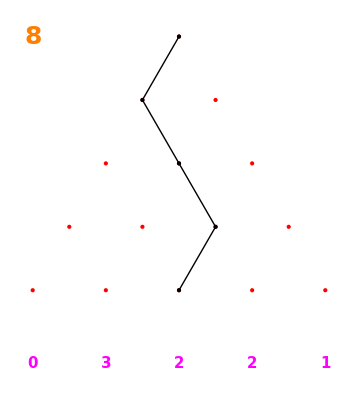

```mathematica
Table[Graphics[
{Text[Style[i,Bold,Orange,25],{-2,0}],
MapThread[Text[Style[#1,Magenta,Bold,15],#2]&,
{Count[Take[pointFinals,i],#]&/@Range[5],
#+{0,-1}&/@Last[board]}],
{Red,Point[#]&/@#}&/@board,
Black,Point[waysCoord[[i]]],
Black,Line[waysCoord[[i]]]},
BaseStyle->{PointSize[0.04]}],
{i,1,Length@waysCoord}]
```

## Задание 4

```mathematica
shariki[size_,n_]:=Block[{pointRoutes,pointFinals,waysCoord,list,board=galt[size]},
pointRoutes=Table[RandomChoice@giveAllRoutes[size],{n}];
pointFinals=Last/@pointRoutes;
waysCoord=ReplacePart[pointRoutes,{i_,j_}:>board[[j,pointRoutes[[i,j]]]]];
list=Table[Graphics[
{Text[Style[i,Bold,Orange,25],{-2,0}],
MapThread[Text[Style[#1,Magenta,Bold,15],#2]&,
{Count[Take[pointFinals,i],#]&/@Range[size],
#+{0,-1}&/@Last[board]}],
{Red,Point[#]&/@#}&/@board,
Black,Point[waysCoord[[i]]],
Black,Line[waysCoord[[i]]]},
BaseStyle->{PointSize[0.04]}],
{i,1,Length@waysCoord}]]
```

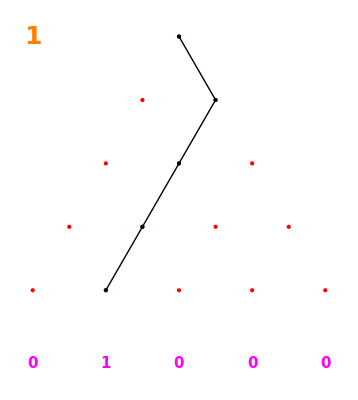
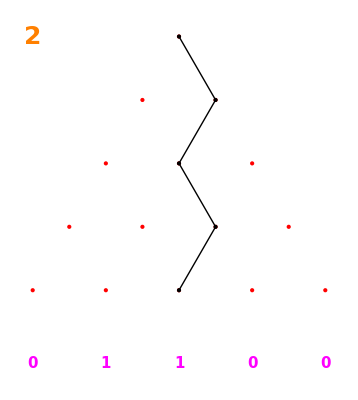
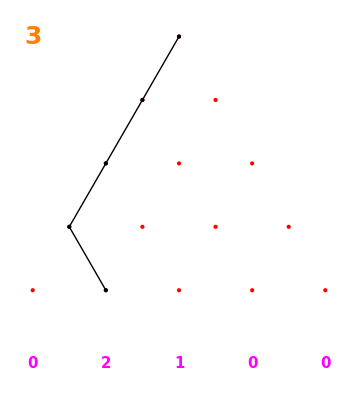
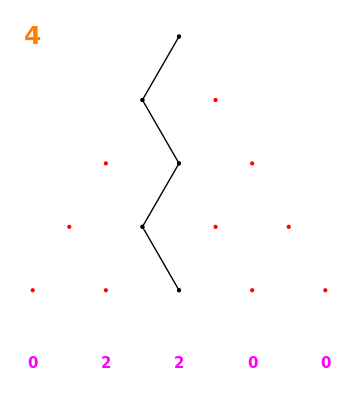

```mathematica
shariki[5,4]
```

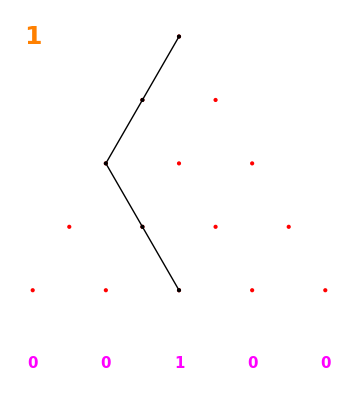
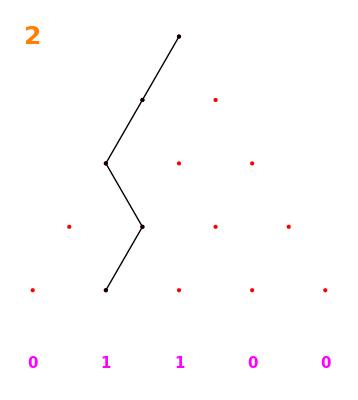
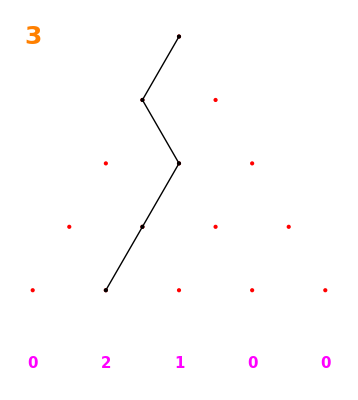
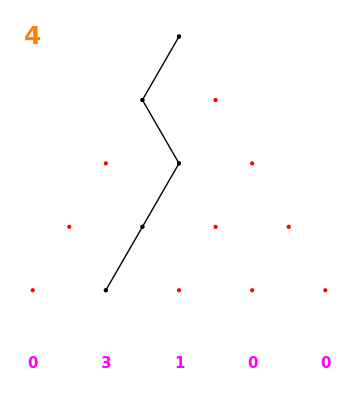
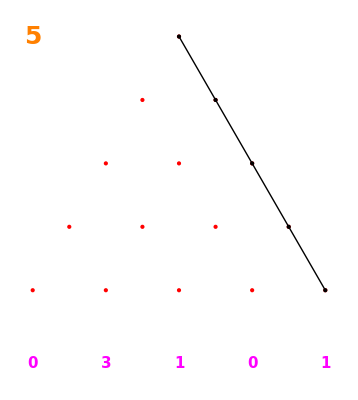
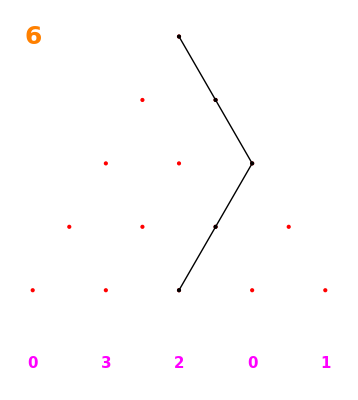
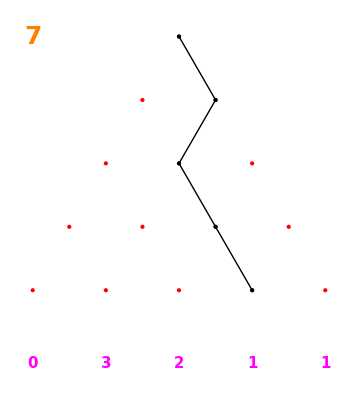
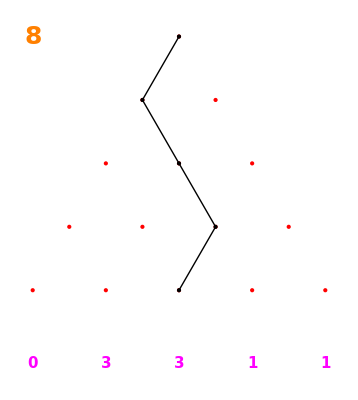

```mathematica
shariki[5,9]
```

```mathematica
ListAnimate[Table[Graphics[
{Text[Style[i,Bold,Orange,25],{-2,0}],
MapThread[Text[Style[#1,Magenta,Bold,15],#2]&,
{Count[Take[pointFinals,i],#]&/@Range[5],
#+{0,-1}&/@Last[board]}],
{Red,Point[#]&/@#}&/@board,
Black,Point[waysCoord[[i]]],
Black,Line[waysCoord[[i]]]},
BaseStyle->{PointSize[0.04]}],
{i,1,Length@waysCoord}]]
```

```mathematica
animateList=shariki[8,13];
```

```mathematica
ListAnimate[animateList,DefaultDuration->18]
```